# Julia Set

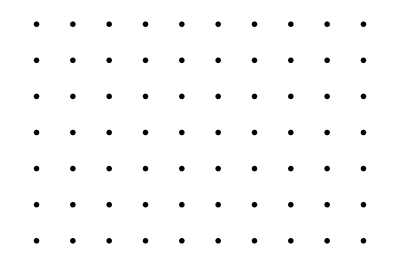

```mathematica
cJulia=Compile[{{c,_Complex},{k,_Complex}},
-Length[
FixedPointList[#^2+k&,c,35,SameTest->(Abs[#2]>2.0&)]
]
];
Show[GraphicsGrid[Table[ListDensityPlot[Table[cJulia[x+y I,a+b I],{y,-1.1,1.1,0.0628},{x,-1.1,1.1,0.0628}],Mesh->False,Frame->False,Axes->False,AspectRatio->1,DisplayFunction->Identity],{b,-1.0,1.0,1/3.},{a,-2.0,1.0,1/3.}]]]
```

```mathematica
Manipulate[cJulia[x+y I,0.3+0.3 I],{x,-1,1},{y,-1,1}]
```

```mathematica
ListDensityPlot[Table[cJulia[x+y I,-1+0.3 I],{y,-1.1,1.1,0.01},{x,-1.1,1.1,0.01}],Mesh->False,Frame->False,Axes->False,AspectRatio->1,DisplayFunction->Identity]
```

-Graphics-